```mathematica
(*Mathematical solution of Rabi Oscillation under the Rotating Wave Approximation (RWA) *)
eqns={x'[t]==I (A2/2) y[t],y'[t]==I (A1 /2)x[t]+I Δ y[t]};
initialConditions={x[0]==1,y[0]==0};
solution=DSolve[{eqns,initialConditions},{x[t],y[t]},t]
```

{{x[t]→(ⅇ^(1/2 ⅈ t (Δ-√(A1 A2+Δ^2))) Δ-ⅇ^(1/2 ⅈ t (Δ+√(A1 A2+Δ^2))) Δ+ⅇ^(1/2 ⅈ t (Δ-√(A1 A2+Δ^2))) √(A1 A2+Δ^2)+ⅇ^(1/2 ⅈ t (Δ+√(A1 A2+Δ^2))) √(A1 A2+Δ^2))/(2 √(A1 A2+Δ^2)),y[t]→-(A1 (ⅇ^(1/2 ⅈ t (Δ-√(A1 A2+Δ^2)))-ⅇ^(1/2 ⅈ t (Δ+√(A1 A2+Δ^2)))))/(2 √(A1 A2+Δ^2))}}

```mathematica
(*Numerical calculation 1: small detuning and small rabi frequency compared to the normal frequency*)
Clear[x];Clear[y](*Ω=0.5,Δ=0.001,ω=ω0=10*)
s=NDSolve[{x'[t]==ⅈ (0.5/2+0.5/2 ⅇ^(-20 ⅈ t)) y[t],y'[t]==ⅈ (0.5/2+0.5/2 ⅇ^(20ⅈ t)) x[t]+ⅈ 0.001 y[t],x[0]==1,y[0]==0  },{x,y},{t,10}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

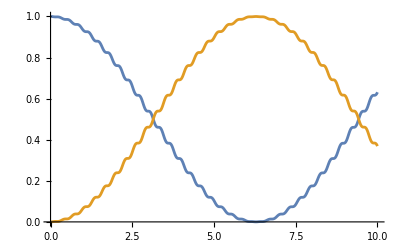

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
Plot[Evaluate[{Abs[x[t]]^2,Abs[y[t]]^2}/. s],{t,0,10},PlotStyle->Automatic]
blochSphere=ParametricPlot3D[{Sin[theta] Cos[phi],Sin[theta] Sin[phi],Cos[theta]},{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Directive[Opacity[0.3],Red],Mesh->None,PlotPoints->50,PlotLabel->"Bloch Sphere"];
thetat[t_]:=2 ArcCos[Abs[x[t]/. s]];
phit[t_]:=Arg[y[t]/. s]-Arg[x[t]/. s];
(*show the traj in the Bloch sphere*)
trajectory=ParametricPlot3D[Evaluate[{Sin[thetat[t]] Cos[phit[t]],Sin[thetat[t]] Sin[phit[t]],Cos[thetat[t]]}]/.s,{t,0,10},PlotStyle->Directive[Opacity[0.3],Blue],Mesh->None,PlotPoints->50];
Show[blochSphere,trajectory,PlotRange->All]
```

```mathematica
(*Numerical calculation 2.A: small detuning and increase the rabi frequency*)
Clear[x];Clear[y](*Ω=1,Δ=0.001,ω=ω0=10*)
s=NDSolve[{x'[t]==ⅈ (1/2+1/2 ⅇ^(-20 ⅈ t)) y[t],y'[t]==ⅈ (1/2+1/2 ⅇ^(20ⅈ t)) x[t]+ⅈ 0.001 y[t],x[0]==1,y[0]==0  },{x,y},{t,10}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

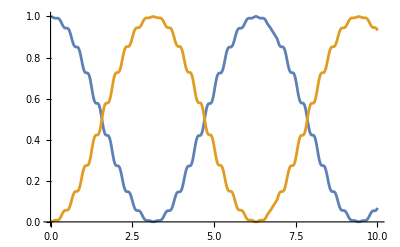

-Graphics3D-

```mathematica
Plot[Evaluate[{Abs[x[t]]^2,Abs[y[t]]^2}/. s],{t,0,10},PlotStyle->Automatic]
blochSphere=ParametricPlot3D[{Sin[theta] Cos[phi],Sin[theta] Sin[phi],Cos[theta]},{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Directive[Opacity[0.3],Red],Mesh->None,PlotPoints->50,PlotLabel->"Bloch Sphere"];
thetat[t_]:=2 ArcCos[Abs[x[t]/. s]];
phit[t_]:=Arg[y[t]/. s]-Arg[x[t]/. s];
(*show the traj in the Bloch sphere*)
trajectory=ParametricPlot3D[Evaluate[{Sin[thetat[t]] Cos[phit[t]],Sin[thetat[t]] Sin[phit[t]],Cos[thetat[t]]}]/.s,{t,0,10},PlotStyle->Directive[Opacity[0.3],Blue],Mesh->None,PlotPoints->50];
Show[blochSphere,trajectory,PlotRange->All]
```

```mathematica
(*Numerical calculation 2.B: small detuning and the same rabi frequency but with the Rotating Wave Approximation*)
Clear[x];Clear[y](*Ω=1,Δ=0.001,ω=ω0=10*)
s=NDSolve[{x'[t]==ⅈ (1/2) y[t],y'[t]==ⅈ (1/2) x[t]+ⅈ 0.001 y[t],x[0]==1,y[0]==0  },{x,y},{t,10}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

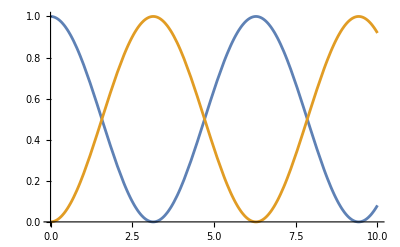

-Graphics3D-

```mathematica
Plot[Evaluate[{Abs[x[t]]^2,Abs[y[t]]^2}/. s],{t,0,10},PlotStyle->Automatic]
blochSphere=ParametricPlot3D[{Sin[theta] Cos[phi],Sin[theta] Sin[phi],Cos[theta]},{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Directive[Opacity[0.3],Red],Mesh->None,PlotPoints->50,PlotLabel->"Bloch Sphere"];
thetat[t_]:=2 ArcCos[Abs[x[t]/. s]];
phit[t_]:=Arg[y[t]/. s]-Arg[x[t]/. s];
(*show the traj in the Bloch sphere*)
trajectory=ParametricPlot3D[Evaluate[{Sin[thetat[t]] Cos[phit[t]],Sin[thetat[t]] Sin[phit[t]],Cos[thetat[t]]}]/.s,{t,0,10},PlotStyle->Directive[Opacity[0.3],Blue],Mesh->None,PlotPoints->50];
Show[blochSphere,trajectory,PlotRange->All]
```

```mathematica
(*Numerical calculation 3: small detuning and larger rabi frequency*)
Clear[x];Clear[y](*Ω=5,Δ=0.001,ω=ω0=10*)
s=NDSolve[{x'[t]==ⅈ (5/2+5/2 ⅇ^(-20 ⅈ t)) y[t],y'[t]==ⅈ (5/2+5/2 ⅇ^(20ⅈ t)) x[t]+ⅈ 0.001 y[t],x[0]==1,y[0]==0  },{x,y},{t,10}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

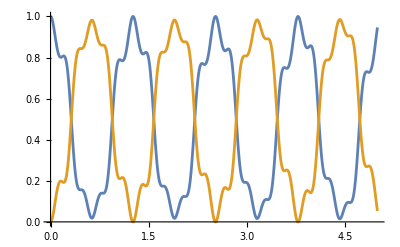

-Graphics3D-

```mathematica
Plot[Evaluate[{Abs[x[t]]^2,Abs[y[t]]^2}/. s],{t,0,5},PlotStyle->Automatic]
blochSphere=ParametricPlot3D[{Sin[theta] Cos[phi],Sin[theta] Sin[phi],Cos[theta]},{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Directive[Opacity[0.3],Red],Mesh->None,PlotPoints->50,PlotLabel->"Bloch Sphere"];
thetat[t_]:=2 ArcCos[Abs[x[t]/. s]];
phit[t_]:=Arg[y[t]/. s]-Arg[x[t]/. s];
(*show the traj in the Bloch sphere*)
trajectory=ParametricPlot3D[Evaluate[{Sin[thetat[t]] Cos[phit[t]],Sin[thetat[t]] Sin[phit[t]],Cos[thetat[t]]}]/.s,{t,0,10},PlotStyle->Directive[Opacity[0.3],Blue],Mesh->None,PlotPoints->50];
Show[blochSphere,trajectory,PlotRange->All]
```

```mathematica
(*Numerical calculation 4.A: small detuning and even larger rabi frequency*)
Clear[x];Clear[y](*Ω=10,Δ=0.001,ω=ω0=10*)
s=NDSolve[{x'[t]==ⅈ (10/2+10/2 ⅇ^(-20 ⅈ t)) y[t],y'[t]==ⅈ (10/2+10/2 ⅇ^(20ⅈ t)) x[t]+ⅈ 0.001 y[t],x[0]==1,y[0]==0  },{x,y},{t,20}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

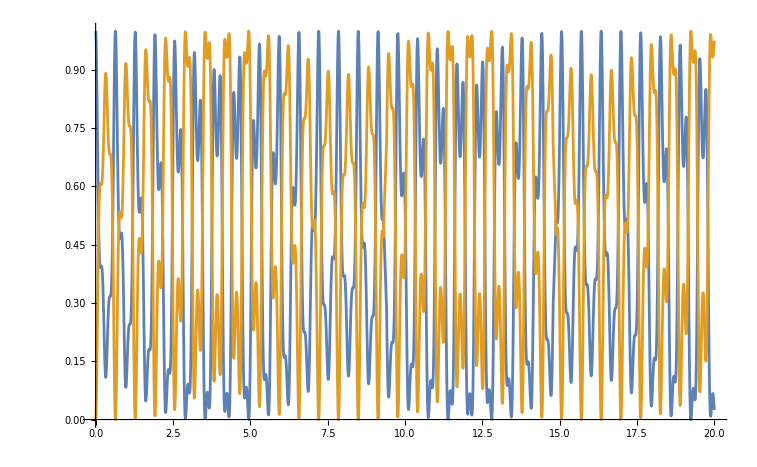

-Graphics3D-

```mathematica
Plot[Evaluate[{Abs[x[t]]^2,Abs[y[t]]^2}/. s],{t,0,20},PlotStyle->Automatic]
blochSphere=ParametricPlot3D[{Sin[theta] Cos[phi],Sin[theta] Sin[phi],Cos[theta]},{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Directive[Opacity[0.3],Red],Mesh->None,PlotPoints->50,PlotLabel->"Bloch Sphere"];
thetat[t_]:=2 ArcCos[Abs[x[t]/. s]];
phit[t_]:=Arg[y[t]/. s]-Arg[x[t]/. s];
(*show the traj in the Bloch sphere*)
trajectory=ParametricPlot3D[Evaluate[{Sin[thetat[t]] Cos[phit[t]],Sin[thetat[t]] Sin[phit[t]],Cos[thetat[t]]}]/.s,{t,0,20},PlotStyle->Directive[Opacity[0.3],Blue],Mesh->None,PlotPoints->50];
Show[blochSphere,trajectory,PlotRange->All]
```

```mathematica
(*Numerical calculation 4.B: small detuning and even larger rabi frequency with the Rotating Wave Approximation*)
Clear[x];Clear[y](*Ω=10,Δ=0.001,ω=ω0=10*)
s=NDSolve[{x'[t]==ⅈ (10/2) y[t],y'[t]==ⅈ (10/2) x[t]+ⅈ 0.001 y[t],x[0]==1,y[0]==0  },{x,y},{t,10}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

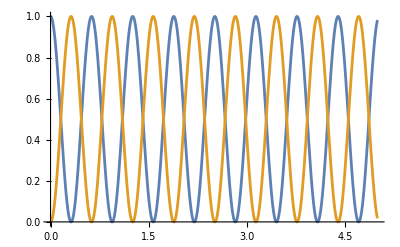

-Graphics3D-

```mathematica
Plot[Evaluate[{Abs[x[t]]^2,Abs[y[t]]^2}/. s],{t,0,5},PlotStyle->Automatic]
blochSphere=ParametricPlot3D[{Sin[theta] Cos[phi],Sin[theta] Sin[phi],Cos[theta]},{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Directive[Opacity[0.3],Red],Mesh->None,PlotPoints->50,PlotLabel->"Bloch Sphere"];
thetat[t_]:=2 ArcCos[Abs[x[t]/. s]];
phit[t_]:=Arg[y[t]/. s]-Arg[x[t]/. s];
(*show the traj in the Bloch sphere*)
trajectory=ParametricPlot3D[Evaluate[{Sin[thetat[t]] Cos[phit[t]],Sin[thetat[t]] Sin[phit[t]],Cos[thetat[t]]}]/.s,{t,0,10},PlotStyle->Directive[Opacity[0.3],Blue],Mesh->None,PlotPoints->50];
Show[blochSphere,trajectory,PlotRange->All]
```

```mathematica
(*Numerical calculation 5: small detuning and  larger rabi frequency in a longer time scale; to see how the RWA breaks over time*)
Clear[x];Clear[y](*Ω=1,Δ=0.001,ω=ω0=10*)
s=NDSolve[{x'[t]==ⅈ (8/2+8/2 ⅇ^(-20 ⅈ t)) y[t],y'[t]==ⅈ (8/2+8/2 ⅇ^(20ⅈ t)) x[t]+ⅈ 0.001 y[t],x[0]==1,y[0]==0  },{x,y},{t,200}];
blochSphere=ParametricPlot3D[{Sin[theta] Cos[phi],Sin[theta] Sin[phi],Cos[theta]},{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Directive[Opacity[0.3],Red],Mesh->None,PlotPoints->50,PlotLabel->"Bloch Sphere"];
thetat[t_]:=2 ArcCos[Abs[x[t]/. s]];
phit[t_]:=Arg[y[t]/. s]-Arg[x[t]/. s];
(*show the traj in the Bloch sphere*)
trajectory=ParametricPlot3D[Evaluate[{Sin[thetat[t]] Cos[phit[t]],Sin[thetat[t]] Sin[phit[t]],Cos[thetat[t]]}]/.s,{t,0,200},PlotStyle->Directive[Opacity[0.3],Blue],Mesh->None,PlotPoints->50];
Show[blochSphere,trajectory,PlotRange->All]
```

-Graphics3D-